# Muon Production in SM - γ-> μ^- μ^+

## Load FeynArts and FormCalc

```mathematica
Quit[]
```

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts-3.11/FeynArts.m"
<<"/home/riccardo/Programs/FormCalc/FormCalc-9.10/FormCalc.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

## Set-up

```mathematica
CKM=IndexDelta;
```

```mathematica
process={V[1]} -> {F[2,{2}], -F[2,{2}]};
```

```mathematica
name="A-mm-SM";
```

```mathematica
SetOptions[InsertFields,Model->"SM",GenericModel->"Lorentz",InsertionLevel->Particles];
SetOptions[Paint,PaintLevel->{Classes},ColumnsXRows->{4,5}];
```

## Tree-Level

## Topologies

> Top. 1 ad/bdcd/0.m, 0 diagrams

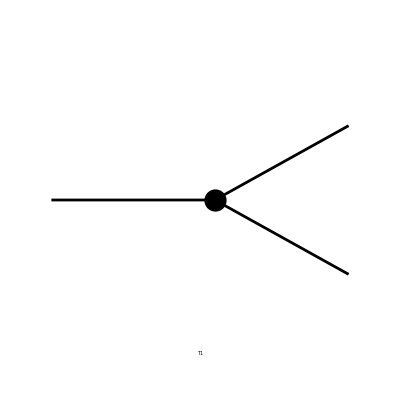

```mathematica
tops=CreateTopologies[0,1->2,Adjacencies->3];
Paint[tops];
```

## Insertions

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

in total: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 1 ad/bdcd/0.m, 0 diagrams

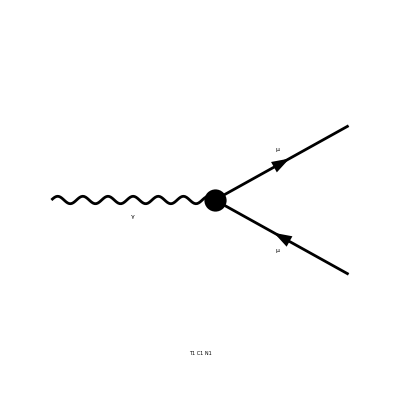

```mathematica
ins=InsertFields[tops, process];
Paint[ins];
```

## Feynman Amplitudes

```mathematica
amp=CreateFeynAmp[ins,AmplitudeLevel->{Particles}];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

## FormCalc results

```mathematica
ClearProcess[]
```

```mathematica
result=CalcFeynAmp[amp]
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-EL (F1+F2)]

```mathematica
UVDivergentPart[result]
```

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0]

## One-Loop

## Topologies

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

> Top. 4 ad/bece/efdfdf.m, 0 diagrams

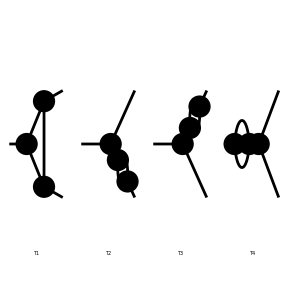

```mathematica
tops1=CreateTopologies[1,1->2,Adjacencies->3,ExcludeTopologies->Tadpoles];
Paint[tops1];
```

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

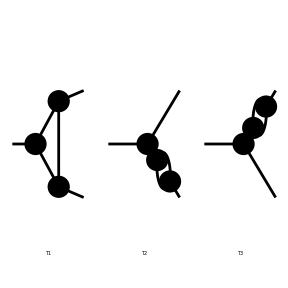

```mathematica
tops1=Delete[tops1,4];
Paint[tops1];
```

## Insertions

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 6 Generic, 8 Classes, 8 Particles insertions

> Top. 2: 2 Generic, 6 Classes, 6 Particles insertions

> Top. 3: 2 Generic, 6 Classes, 6 Particles insertions

in total: 10 Generic, 20 Classes, 20 Particles insertions

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

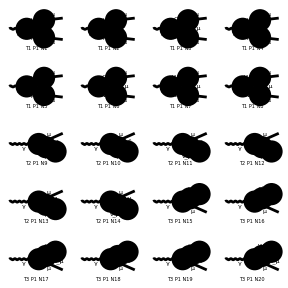

```mathematica
ins1=InsertFields[tops1, process];
Paint[ins1, PaintLevel->{Particles}];
```

## Feynman Amplitudes

```mathematica
amp1=CreateFeynAmp[ins1,AmplitudeLevel->{Particles}];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 8 Particles amplitudes

> Top. 2: 6 Particles amplitudes

> Top. 3: 6 Particles amplitudes

in total: 20 Particles amplitudes

## FormCalc results

```mathematica
result1=CalcFeynAmp[amp1];
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

## Amplitude manipulations

## Amplitude manipulation tools

```mathematica
selectFeynAmp[amp_,i_Integer/;i≥0]:=amp[[0]][amp[[i]]]
```

```mathematica
calcFeynAmp[amp_,i_Integer/;i≥0]:=CalcFeynAmp[amp[[0]][amp[[i]]]]
```

```mathematica
calcFeynAmpList[amp_]:=Map[CalcFeynAmp[amp[[0]][#]]&,amp]
```

## Computations

```mathematica
Length[amp1]
```

20

```mathematica
result1List=calcFeynAmpList[amp1]/.result1List[[0]]->List;
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

```mathematica
uvDiv=Map[UVDivergentPart,result1List]//Simplify
```

FeynAmpList[Process→{{V[1],p1,0,{}}}→{{F[2,{2}],k1,MM,{-Charge,LeptonNumber}},{-F[2,{2}],k2,MM,{Charge,-LeptonNumber}}},Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(Alfa Divergence EL (F1+F2) MM2)/(32 MW2 π SW2)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(Alfa Divergence EL (F1+F2) MM2)/(32 MW2 π SW2)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(Alfa Divergence EL F2 MM2)/(16 MW2 π SW2)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(Alfa Divergence EL (F1+F2))/(4 π)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(Alfa Divergence EL Sub61)/(16 CW2 π)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(3 Alfa Divergence EL F1)/(8 π SW2)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][(3 Alfa Divergence EL (F1+F2) MM2^2 Den[MM2,MM2])/(16 MW2 π SW2)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(Alfa Divergence EL (F1+F2) MM2^2 Den[MM2,MM2])/(16 MW2 π SW2)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][(Alfa Divergence EL (F1+F2) MM2^2 Den[MM2,MM2])/(16 MW2 π SW2)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(3 Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(2 π)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][(Alfa Divergence EL (F1+F2) MM2 (16+Sub16-32 SW2) Den[MM2,MM2])/(16 CW2 π)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][(Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(8 π SW2)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][(3 Alfa Divergence EL (F1+F2) MM2^2 Den[MM2,MM2])/(16 MW2 π SW2)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(Alfa Divergence EL (F1+F2) MM2^2 Den[MM2,MM2])/(16 MW2 π SW2)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][(Alfa Divergence EL (F1+F2) MM2^2 Den[MM2,MM2])/(16 MW2 π SW2)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(3 Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(2 π)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][(Alfa Divergence EL (F1+F2) MM2 (16+Sub16-32 SW2) Den[MM2,MM2])/(16 CW2 π)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][(Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(8 π SW2)]]

```mathematica
uvDivL=Map[#[[1]]&,uvDiv]/.uvDivL[[0]]->List
```

{-(Alfa Divergence EL (F1+F2) MM2)/(32 MW2 π SW2),-(Alfa Divergence EL (F1+F2) MM2)/(32 MW2 π SW2),-(Alfa Divergence EL F2 MM2)/(16 MW2 π SW2),-(Alfa Divergence EL (F1+F2))/(4 π),-(Alfa Divergence EL Sub61)/(16 CW2 π),0,0,-(3 Alfa Divergence EL F1)/(8 π SW2),(3 Alfa Divergence EL (F1+F2) MM2^2 Den[MM2,MM2])/(16 MW2 π SW2),-(Alfa Divergence EL (F1+F2) MM2^2 Den[MM2,MM2])/(16 MW2 π SW2),(Alfa Divergence EL (F1+F2) MM2^2 Den[MM2,MM2])/(16 MW2 π SW2),-(3 Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(2 π),(Alfa Divergence EL (F1+F2) MM2 (16+Sub16-32 SW2) Den[MM2,MM2])/(16 CW2 π),(Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(8 π SW2),(3 Alfa Divergence EL (F1+F2) MM2^2 Den[MM2,MM2])/(16 MW2 π SW2),-(Alfa Divergence EL (F1+F2) MM2^2 Den[MM2,MM2])/(16 MW2 π SW2),(Alfa Divergence EL (F1+F2) MM2^2 Den[MM2,MM2])/(16 MW2 π SW2),-(3 Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(2 π),(Alfa Divergence EL (F1+F2) MM2 (16+Sub16-32 SW2) Den[MM2,MM2])/(16 CW2 π),(Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(8 π SW2)}

## Diagram Selection

## Z Boson

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

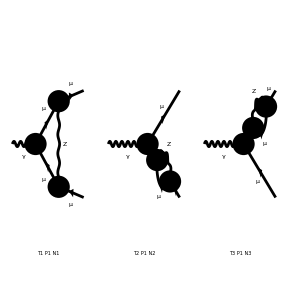

```mathematica
insZ=DiagramSelect[ins1,!FreeQ[#,V[2]]&];
Paint[insZ,PaintLevel->{Particles}];
```

```mathematica
ampZ=CreateFeynAmp[insZ,AmplitudeLevel->{Particles}];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

in total: 3 Particles amplitudes

```mathematica
resultZ=CalcFeynAmp[ampZ]
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][1/(CW2 π)Alfa EL (Sub61 (Finite/16-1/8 B0i[bb0,MM2,MM2,MZ2]+1/4 C0i[cc00,0,MM2,MM2,MM2,MM2,MZ2])-1/8 Sub151 C0i[cc2,0,MM2,MM2,MM2,MM2,MZ2]+1/4 MM Pair1 (Sub31 C0i[cc12,0,MM2,MM2,MM2,MM2,MZ2]+Sub41 C0i[cc22,0,MM2,MM2,MM2,MM2,MZ2])-(F1+F2) MM2 ((Finite Sub11)/8-2 (1-2 SW2) B0i[bb0,MM2,MM2,MZ2]+1/4 Sub16 B0i[bb1,MM2,MM2,MZ2]) Den[MM2,MM2])]

```mathematica
UVDivergentPart[resultZ]//Simplify
```

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(Alfa Divergence EL (Sub61-2 (F1+F2) MM2 (16+Sub16-32 SW2) Den[MM2,MM2]))/(16 CW2 π)]

```mathematica
resultZList=calcFeynAmpList[ampZ]/.resultZList[[0]]->List;
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

```mathematica
uvDivZ=Map[UVDivergentPart,resultZList]//Simplify
```

{Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(Alfa Divergence EL Sub61)/(16 CW2 π)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][(Alfa Divergence EL (F1+F2) MM2 (16+Sub16-32 SW2) Den[MM2,MM2])/(16 CW2 π)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][(Alfa Divergence EL (F1+F2) MM2 (16+Sub16-32 SW2) Den[MM2,MM2])/(16 CW2 π)]}

```mathematica
uvDivZL=Map[#[[1]]&,uvDivZ]/.uvDivZ[[0]]->List
```

{-(Alfa Divergence EL Sub61)/(16 CW2 π),(Alfa Divergence EL (F1+F2) MM2 (16+Sub16-32 SW2) Den[MM2,MM2])/(16 CW2 π),(Alfa Divergence EL (F1+F2) MM2 (16+Sub16-32 SW2) Den[MM2,MM2])/(16 CW2 π)}

## W Boson

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

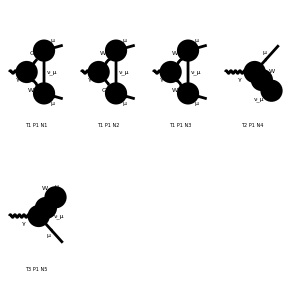

```mathematica
insW=DiagramSelect[ins1,!FreeQ[#,V[3]]&];
Paint[insW,PaintLevel->{Particles}];
```

```mathematica
ampW=CreateFeynAmp[insW,AmplitudeLevel->{Particles}];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

in total: 5 Particles amplitudes

```mathematica
resultW=CalcFeynAmp[ampW];
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

```mathematica
UVDivergentPart[resultW]//Simplify
```

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][(Alfa Divergence EL (-3 F1+2 (F1+F2) MM2 Den[MM2,MM2]))/(8 π SW2)]

```mathematica
resultWList=calcFeynAmpList[ampW]/.resultWList[[0]]->List;
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

```mathematica
uvDivW=Map[UVDivergentPart,resultWList]//Simplify
```

{Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(3 Alfa Divergence EL F1)/(8 π SW2)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][(Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(8 π SW2)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][(Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(8 π SW2)]}

```mathematica
uvDivWL=Map[#[[1]]&,uvDivW]/.uvDivW[[0]]->List
```

{0,0,-(3 Alfa Divergence EL F1)/(8 π SW2),(Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(8 π SW2),(Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(8 π SW2)}